2

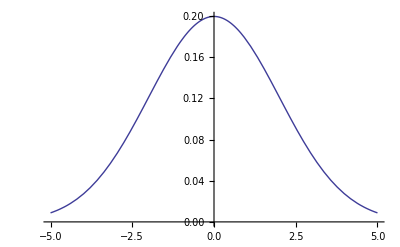

```mathematica
SD=2
Plot[{PDF[NormalDistribution[0,SD],x]},{x,-5,5}]
```

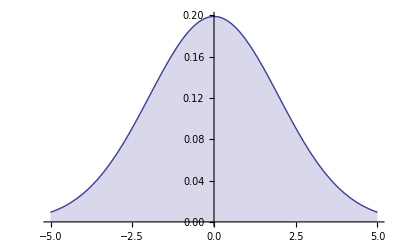

```mathematica
Plot[{PDF[StudentTDistribution[0,SD,100],x]},{x,-5,5},Filling->Axis]
```

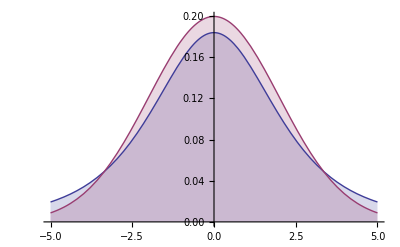

```mathematica
Plot[{PDF[StudentTDistribution[0,SD,3],x],PDF[NormalDistribution[0,SD],x]},{x,-5,5},Filling->Axis]
```

```mathematica
SD
```

2

```mathematica
Integrate[{(ⅇ^(-x^2/(2*SD^2)))/(SD*√(2 π))},{x,-10,10}]
N[%]
```

{Erf[5/(√2)]}

{0.999999}

```mathematica
yRange=1
```

1

```mathematica
Integrate[{(ⅇ^(-x^2/2))/(√(2 π))},{x,-yRange,yRange}]
N[%]
```

{Erf[1/(√2)]}

{0.682689}

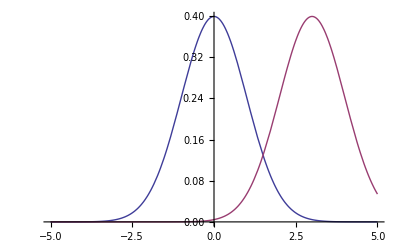

```mathematica
Plot[{PDF[NormalDistribution[0,1.0],x],
PDF[NormalDistribution[3,1],x]},{x,-5,5}]
```

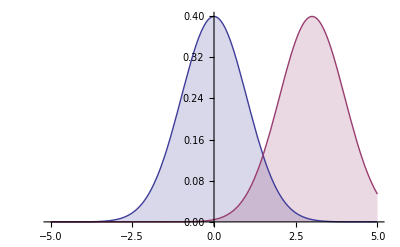

```mathematica
Plot[{PDF[NormalDistribution[0,1],x],
PDF[NormalDistribution[3,1],x]},{x,-5,5},Filling->Axis]
```

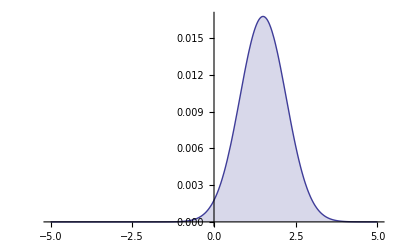

```mathematica
Plot[PDF[NormalDistribution[0,1],x]*
PDF[NormalDistribution[3,1],x],{x,-5,5},Filling->Axis]
```

```mathematica
MeanSeparation=2
```

2

```mathematica
Integrate[PDF[NormalDistribution[0,1],x]*
PDF[NormalDistribution[MeanSeparation,1],x],{x,-100,100}]
```

(Erf[99]+Erf[101])/(4 ⅇ √π)

```mathematica
N[%]/2
```

0.0518884

```mathematica
`
```